```mathematica
$Assumptions=Element[e0amp,Reals]&&Element[px0,Reals]&&Element[py0,Reals]&&Element[pz0,Reals]&&Element[tem,Reals];
e0={0,e0amp,0};b0={0,0,e0amp};p0={px0,py0,0};
ep=e0*tem;
utemp=p0+ep;
gamtem=tem/(√(1+utemp[[1]]^2+utemp[[2]]^2+utemp[[3]]^2));
bp=b0*gamtem;
pnew=utemp+Cross[utemp,bp];
bp=2 bp/(1+bp[[1]]^2+bp[[2]]^2+bp[[3]]^2)//FullSimplify;
utemp=utemp+Cross[pnew,bp]//FullSimplify;
pfinal=utemp+ep//FullSimplify
```

{(px0^3+px0 (1+py0^2+2 e0amp py0 tem)+2 e0amp tem (py0+e0amp tem) √(1+px0^2+(py0+e0amp tem)^2))/(1+px0^2+py0^2+2 e0amp py0 tem+2 e0amp^2 tem^2),e0amp tem+(py0^3+3 e0amp py0^2 tem+py0 (1+px0^2+2 e0amp^2 tem^2)+e0amp tem (1+px0^2-2 px0 √(1+px0^2+(py0+e0amp tem)^2)))/(1+px0^2+py0^2+2 e0amp py0 tem+2 e0amp^2 tem^2),0}

```mathematica
ans=Solve[(pfinal+p0)/2=={pxtrue,0,0},{px0,py0}]
```

{{px0→pxtrue,py0→1/2 (-2 e0amp tem-√2 √(-1-pxtrue^2-√(1+2 pxtrue^2+pxtrue^4+4 e0amp^2 pxtrue^2 tem^2)))},{px0→pxtrue,py0→1/2 (-2 e0amp tem+√2 √(-1-pxtrue^2-√(1+2 pxtrue^2+pxtrue^4+4 e0amp^2 pxtrue^2 tem^2)))},{px0→pxtrue,py0→1/2 (-2 e0amp tem-√2 √(-1-pxtrue^2+√(1+2 pxtrue^2+pxtrue^4+4 e0amp^2 pxtrue^2 tem^2)))},{px0→pxtrue,py0→1/2 (-2 e0amp tem+√2 √(-1-pxtrue^2+√(1+2 pxtrue^2+pxtrue^4+4 e0amp^2 pxtrue^2 tem^2)))}}

Now we know we can set px0 = pxtrue.  The solution is much more simple now.

```mathematica
ans=Solve[(pfinal[[2]]+p0[[2]])/2==0,{py0}]//FullSimplify
```

{{py0→-ⅈ √(1+px0^2)-e0amp tem},{py0→ⅈ √(1+px0^2)-e0amp tem},{py0→-e0amp tem-(ⅈ √(1+px0^2+√((1+px0^2)^2+4 e0amp^2 px0^2 tem^2)))/(√2)},{py0→-e0amp tem+(ⅈ √(1+px0^2+√((1+px0^2)^2+4 e0amp^2 px0^2 tem^2)))/(√2)},{py0→-e0amp tem-(√(-1-px0^2+√((1+px0^2)^2+4 e0amp^2 px0^2 tem^2)))/(√2)},{py0→-e0amp tem+(√(-1-px0^2+√((1+px0^2)^2+4 e0amp^2 px0^2 tem^2)))/(√2)}}

```mathematica
ans/.{px0->3.,tem->0.5*0.14/-1.0,e0amp->5.}
```

{{py0→0.35-3.16228 ⅈ},{py0→0.35+3.16228 ⅈ},{py0→0.35-3.17947 ⅈ},{py0→0.35+3.17947 ⅈ},{py0→0.0197568},{py0→0.680243}}

```mathematica
soln=py0/.ans[[5]]
```

-e0amp tem-(√(-1-px0^2+√((1+px0^2)^2+4 e0amp^2 px0^2 tem^2)))/(√2)

```mathematica
fullsoln=soln/.{tem->-dt/2}
```

(dt e0amp)/2-(√(-1-px0^2+√(dt^2 e0amp^2 px0^2+(1+px0^2)^2)))/(√2)

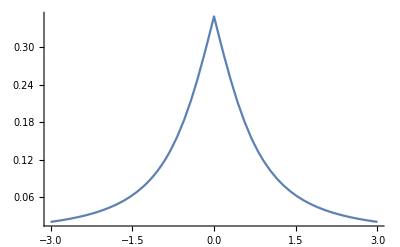

```mathematica
Plot[(fullsoln/.{dt->0.14,e0amp->5.}),{px0,-3,3},PlotRange->{0,All}]
```